# Arc Length Calculations

## Eric Moyer

28 March 2012

The functions that will be combined through union to create new functions need their arc-lengths calculated so that the samples are unformly distributed throughout all the points in the relations.

Since I want to find the arc length when the function is confined to a box, this could be seen as the minimum of the arc lengths when the integral is taken over 0,1 for x and over 0,1 for y. For functions that are not invertible, I'll have to do a parametric version and find the version of the parameter for the last coordinate in the box.

## Code

```mathematica
arcL[f_]:=With[{dx=D[f,x]},Integrate[Sqrt[1+(dx)^2],{x,0,1}]]
```

## Linear

```mathematica
arcL[x]
```

√2

```mathematica
linArcL[a_,b_]:=Min[arcL[a x+b],arcL[(x-b)/a]]
```

```mathematica
linArcL[a,b]
```

Min[√(1+1/a^2),√(1+a^2)]

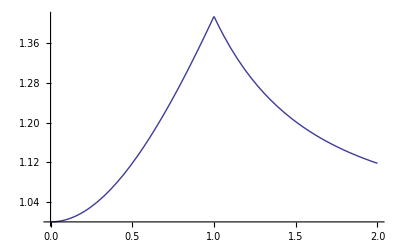

```mathematica
Plot[linArcL[a,b],{a,0,2},PlotRange->All]
```

## Parabolic

Here I just figure the arc length for the single parabola I will examine.

```mathematica
arcL[4(x-1/2)^2]
```

1/8 (4 √17+ArcSinh[4])

```mathematica
N[1/8 (4 √17+ArcSinh[4]),20]
```

2.3233918812164679367

## Cubic

For the cubic, I will assume that the parameters have been chosen so that the y values do not escape from the box on the interval 0,1. All of the functions I am interested in meet that criterion.

Then, I can just take the integral over the 0,1 x interval, no need to worry about inverting.

The following gives the coordinates of the zero derivatives. The function cannot change directions other than there.

```mathematica
Solve[D[a+x(b+x(c +d x)),x]==0,{x}]
```

{{x→(-c-√(c^2-3 b d))/(3 d)},{x→(-c+√(c^2-3 b d))/(3 d)}}

I could check the assumption by checking whether the cubic intercepts the box on the three intervals defined by these two points (by checking the heights of the end-pointssince the function is monotonic between them) and then checking the locations of the points. But that is complex. I think it a better use of time to just document my assumption and leave it to the user to ensure that it holds.

```mathematica
arcL[a+x(b+x(c +d x))]
```

$Aborted

I realized that I don't even need to calculate the arc length for the cubic - I never combine the cubic with anything else in my experiment plan.

## Sine

I have several functions that are (1+sin(f(x) x))/2 and these I do combine

```mathematica
arcL[(1+Sin[k x])/2]
```

If[(((4+k^2) Csc[k]^2)/k^2∉Reals||Re[((4+k^2) Csc[k]^2)/k^2]≤0||Re[((4+k^2) Csc[k]^2)/k^2]≥1)&&(((8+k^2+k^2 Cos[2 k]) Csc[k]^2)/k^2∉Reals||Re[((8+k^2+k^2 Cos[2 k]) Csc[k]^2)/k^2]≤-2||Re[((8+k^2+k^2 Cos[2 k]) Csc[k]^2)/k^2]≥0)&&k^2≠-4&&k^2 Cos[k]^2≠-4,(√(8+k^2+k^2 Cos[2 k]) EllipticE[k,k^2/(4+k^2)])/(2 k √((8+k^2+k^2 Cos[2 k])/(4+k^2))),Integrate[√(1+1/4 k^2 Cos[k x]^2),{x,0,1},Assumptions→k^2==-4||k^2 Cos[k]^2==-4||(((4+k^2) Csc[k]^2)/k^2∈Reals&&0<Re[((4+k^2) Csc[k]^2)/k^2]<1)||(((8+k^2+k^2 Cos[2 k]) Csc[k]^2)/k^2∈Reals&&-2<Re[((8+k^2+k^2 Cos[2 k]) Csc[k]^2)/k^2]<0)]]

That expression is way too complex.

All of the cases I am interested in, we have small, positive integral multiples of Pi.

```mathematica
sinFunc[k_,x_]:=(1+Sin[k Pi x])/2
```

```mathematica
dSinFunc[k_,x_]:=D[sinFunc[k,x],x]
```

```mathematica
(dSinFunc[k,x])^2
```

1/4 k^2 π^2 Cos[k π x]^2

```mathematica
Integrate[Sqrt[1+1/4 k^2 π^2 Cos[k π x]^2],{x,0,1},Assumptions->k∈Integers]
```

$Aborted

The above took too long.

Instead, I will use symmetry. The sine function is symmetric on the quarter period. So, the arc lengths should be the sum of the quarter period lengths times a scale factor.

First, the full period length

```mathematica
lengthForKPi[k_Integer]:=Integrate[Sqrt[1+1/4 k^2 π^2 Cos[k π x]^2],{x,0,1}]
```

```mathematica
N[lengthForKPi[2]]
```

2.30489

Now the quarter period length

```mathematica
N[Integrate[Sqrt[1+1/4 2^2 π^2 Cos[2 π x]^2],{x,0,1/4}]]
```

0.576223

Indeed the symmetry holds.

```mathematica
2.3048926613536906/0.5762231653384227
```

4.

Now, let's see whether there is a scale factor

```mathematica
lengthForKPi[4]/lengthForKPi[2]
```

(√((1+4 π^2)/(1+π^2)) EllipticE[(4 π^2)/(1+4 π^2)])/EllipticE[π^2/(1+π^2)]

```mathematica
FullSimplify[%]
```

(√(4-3/(1+π^2)) EllipticE[(4 π^2)/(1+4 π^2)])/EllipticE[π^2/(1+π^2)]

Oops, no obvious scale factor.

Let's check to see whether something is hiding in the notation that gets revealed when we convert to numbers.

```mathematica
N[lengthForKPi[4]/lengthForKPi[2]]
```

1.81712

```mathematica
N[lengthForKPi[8]/lengthForKPi[2]]
```

3.5194

```mathematica
N[lengthForKPi[8]/lengthForKPi[4]]
```

1.93679

Nope, nothing hiding. time to cut my losses and just calculate for special cases.

### 2π

```mathematica
N[lengthForKPi[2],20]
```

2.3048926613536912

### 3π

```mathematica
N[lengthForKPi[3],20]
```

3.2313069278203268128

### 4π

```mathematica
N[lengthForKPi[4],20]
```

4.1882752036984339214

### 10π

```mathematica
N[lengthForKPi[10],20]
```

10.094000666202479279